# CPS Final Project - Rummikub

Cat Appelman and Lars Hebenstiel
Instructors: Bruce Kessler and Huanjing Wang
MATH/CS 371 - 001

## Project Proposal

### On Screen design should look something like this:

Main “Main Menu” screen will have buttons “Instructions” and “Play”. The “Instructions” button will display how to play the game along with the rules. The “Play” button will display a “Set Up” screen.
-Graphics-
“Set Up” scree n will allow the user to choose how many human players will be playing, the number of AI’s, and the difficulty level of the AI’s. Once the desired options have been selected, the user can press the “Start” button, which will take the user to a play screen.
-Graphics-
The play screen is where all of the user interaction happens.
-Graphics-

### New Increments

#### Increment 1

We will create a single AI  that can play Rummikub with single melds. We will also make an interface separately with working graphics.

#### Increment 2

We will combine AI and Interface to make the game playable between people and AIs, again only with single melds.

#### Increment 3

We will do both of the above for multi-melding.

#### Why we changed increments

We realized the way our increments were structured previously did not make sense for how we ended up attacking the project. Previous increments also did not give us reasonable amounts of time for completing tasks. Once we started working, we combined certain parts of the original “Levels” into one increment while leaving other parts for later increments, making the increments much more balanced.  For example, the AI took longer than we originally planned so we dedicated a new increment entirely to the AI. Part of this increment was dedicated to graphics as well, so there was an equal amount of work between the two of us.

## Code

```mathematica
rummikub[];
MemoryInUse[]
Share[]
MaxMemoryUsed[]
```

61998048

90504

80701792

```mathematica
(*These two options are here for debug purposes. There should be no PrintToConsole statements anywhere, but if we want to use them, this is here so we can call up and put away the console.*)
SetOptions[MessagesNotebook[],Visible-> True];
```

```mathematica
SetOptions[MessagesNotebook[],Visible-> False];
```

```mathematica
(*This is here to attempt to fix memory stuff*)
MemoryInUse[]
Share[]
MaxMemoryUsed[]
```

63843088

108424

86814944

### Encore

```mathematica
Clear[rummikub]
(*Use this function to play the game*)
rummikub[]:=
Deploy@CreateWindow[
CreateDialog[
DynamicModule[
{gamestate="Main Menu",
player1tiles={},player2tiles={},player3tiles={},player4tiles={},
player1state,player2state,player3state,player4state,fmove,
player1firstmove=True,player2firstmove=True,player3firstmove=True,player4firstmove=True,
numOfHumanPlayers=1,numOfAIPlayers=1,numOfTotalPlayers=2,currentPlayer=1,width=160,height=90,
bag, board,mousepos,rackPressIndex,rackPressPos,tileAlreadyThere,pressIndex,pressPos,savedRack,savedBoard,
covered=True,currplayerstate,res,madeMove=False,winner=-1,inProgress=False,
player1name="Player 1",player2name="Player 2",player3name="Player 3",player4name="Player 4",thinking=False,

selectedTile=0,

lightbuttoncolor=Lighter@Lighter@Gray,
darkbuttoncolor=Lighter@Gray,

mainMenuButtons = {makeButton[{65,35},{95,44},"Play",Gray,White,"RoundRect",60,"Alegreya SC"],
makeButton[{60,7},{100,16},"Rules",Gray,White,"RoundRect",60,"Alegreya SC"],
makeButton[{55,21},{105,30},"Instructions",Gray,White,"RoundRect",60,"Alegreya SC"],
makeButton[{1,1},{16,8},"Close",Gray,White,"RoundRect",40,"Alegreya SC"],
makeButton[{135,1},{159,8},"Resume Game",Gray,White,"RoundRect",30,"Alegreya SC"]
},

instructionsButtons = {makeButton[{1,1},{20,10},"Go Back",Lighter@Gray,White,"LArrow",30,"Alegreya SC"]},

setupButtons = condensedSetupButtonsInit[],

playButtons = {
makeButton[{130,1},{145,12},"Next Player",RGBColor[94/255,178/225,101/255],White,"RArrow",20,"Alegreya SC"],
makeButton[{130,13},{145,19},"Reset",Lighter@Gray,White,"RoundRect",30,"Alegreya SC"],
makeButton[{130,21},{145,27},"Draw",RGBColor[203/255,119/225,221/255],White,"Rectangle",30,"Alegreya SC"],
makeButton[{146,2},{159,27},"Return\nTo\nMain\nMenu",Lighter@Lighter@Blue,White,"Rectangle",28,"Alegreya SC"]
},
boardTiles,rackTiles
},
Dynamic@Switch[gamestate,"Main Menu",
EventHandler[
mainMenuGraphics[width,height,mainMenuButtons]
,
{
"MouseClicked":> (
(*Depending on which button is pressed, do different things*)
mousepos=MousePosition@"Graphics";
If[buttonPressed[mainMenuButtons[[2]],mousepos],gamestate="Rules"];
If[buttonPressed[mainMenuButtons[[3]],mousepos],gamestate="Instructions"];
If[buttonPressed[mainMenuButtons[[1]],mousepos],gamestate="Setup"];
If[buttonPressed[mainMenuButtons[[4]],mousepos], DialogReturn[];NotebookClose[]];
If[inProgress && buttonPressed[mainMenuButtons⟦5⟧,mousepos],If[!StringQ@winner,gamestate="Play"; covered=True,gamestate="Won"]];
)
}
]
,
"Instructions"
,
EventHandler[
instructionsGraphics[width,height,instructionsButtons]
,
{
"MouseClicked":> (If[buttonPressed[instructionsButtons[[1]],MousePosition@"Graphics"],gamestate="Main Menu"])
}
]
,
"Rules"
,
EventHandler[
rulesGraphics[width,height,instructionsButtons]
,
{
"MouseClicked":> (If[buttonPressed[instructionsButtons[[1]],MousePosition@"Graphics"],gamestate="Main Menu"])
}
]
,
"Won"
,
EventHandler[
winGraphics[width,height,playButtons,boardTiles, rackTiles,selectedTile,currentPlayer,{player1name,player2name,player3name,player4name},covered,Switch[currentPlayer,1,player1state,2,player2state,3,player3state,4,player4state],{Length@bag,Length@Select[player1tiles,#≠0&],Length@Select[player2tiles,#≠0&],Length@Select[player3tiles,#≠0&],Length@Select[player4tiles,#≠0&]},numOfTotalPlayers,winner]
,
{
"MouseClicked":> (
gamestate="Main Menu";
If[buttonPressed[instructionsButtons⟦1⟧,MousePosition@"Graphics"],gamestate="Main Menu"]
)
}
]
,
"Setup"
,
EventHandler[
Show[
{
setupGraphics[width,height,setupButtons]
,
Graphics[
{
Inset[InputField[Dynamic@player1name,String,FieldSize->{14,1.1}],{127.5,55},BaseStyle->FontSize->25],
Inset[InputField[Dynamic@player2name,String,FieldSize->{14,1.1}],{127.5,50},BaseStyle->FontSize->25],
Inset[InputField[Dynamic@player3name,String,FieldSize->{14,1.1}],{127.5,45},BaseStyle->FontSize->25],
Inset[InputField[Dynamic@player4name,String,FieldSize->{14,1.1}],{127.5,40},BaseStyle->FontSize->25]
}
]
}
]
,
{
"MouseClicked":> (
condensedSetupButtons[setupButtons,MousePosition@"Graphics",lightbuttoncolor,darkbuttoncolor,numOfHumanPlayers,numOfAIPlayers];
If[buttonPressed[setupButtons[[11]],MousePosition@"Graphics"],
gamestate="Main Menu";
];
If[buttonPressed[setupButtons[[12]],MousePosition@"Graphics"],
If[numOfHumanPlayers+numOfAIPlayers < 5 &&numOfHumanPlayers+numOfAIPlayers>1,
numOfTotalPlayers=numOfHumanPlayers+numOfAIPlayers;
gamestate="Play";

(*Reset vars*)
board={};
player1tiles={};
player2tiles={};
player3tiles={};
player4tiles={};
currentPlayer=1;
player1firstmove=True;
player2firstmove=True;
player3firstmove=True;
player4firstmove=True;
winner=-1;

(*Set player states*)
Switch[numOfHumanPlayers,
0,Switch[numOfAIPlayers,
2,player1state="AI";player2state="AI";,
3,player1state="AI";player2state="AI";player3state="AI";,
4,player1state="AI";player2state="AI";player3state="AI";player4state="AI";
],
1,player1state="Human";Switch[numOfAIPlayers,
1,player2state="AI",
2,player2state="AI";player3state="AI";,
3,player2state="AI";player3state="AI";player4state="AI"
],
2,player1state="Human";player2state="Human";Switch[numOfAIPlayers,
1,player3state="AI";,
2,player3state="AI";player4state="AI";
],
3,player1state="Human";player2state="Human";player3state="Human";Switch[numOfAIPlayers,
1,player4state="AI";
],
4,player1state="Human";player2state="Human";player3state="Human";player4state="Human";
];

(*Initialize bag and give players tiles*)
bag=Join[Range@53,Range@53];
If[numOfTotalPlayers>0,Do[AppendTo[player1tiles,pickTile[bag]],14];player1tiles =Join[player1tiles,ConstantArray[0,16]]];
If[numOfTotalPlayers>1,Do[AppendTo[player2tiles,pickTile[bag]],14];player2tiles =Join[player2tiles,ConstantArray[0,16]]];
If[numOfTotalPlayers>2,Do[AppendTo[player3tiles,pickTile[bag]],14];player3tiles =Join[player3tiles,ConstantArray[0,16]]];
If[numOfTotalPlayers>3,Do[AppendTo[player4tiles,pickTile[bag]],14];player4tiles =Join[player4tiles,ConstantArray[0,16]]];

rackTiles=convertRackToView[player1tiles];
board={};
boardTiles=convertBoardToView[board];
savedRack=rackTiles;
savedBoard=boardTiles;
covered=True;
inProgress=True;
]
]
)
},
PassEventsDown->True
]
,
"Play"
,
EventHandler[
Show[
playGraphics[width,height,playButtons,boardTiles, rackTiles,selectedTile,currentPlayer,{player1name,player2name,player3name,player4name},covered,Switch[currentPlayer,1,player1state,2,player2state,3,player3state,4,player4state],{Length@bag,Length@Select[player1tiles,#≠0&],Length@Select[player2tiles,#≠0&],Length@Select[player3tiles,#≠0&],Length@Select[player4tiles,#≠0&]},numOfTotalPlayers]
,
Graphics[If[thinking,Style[Text["Thinking",{80,31.2}],White,FontSize->18,FontFamily->"Alegreya SC"]]]]
,
{
"MouseClicked":> (
mousepos=MousePosition@"Graphics";
(*First check if the the return to main button was pressed, if not, then actually do stuff.*)
If[buttonPressed[playButtons[[4]],mousepos],gamestate="Main Menu"];

If[covered,

Switch[
currentPlayer,
1,currplayerstate=player1state,
2,currplayerstate=player2state,
3,currplayerstate=player3state,
4,currplayerstate=player4state
];

If[currplayerstate=="Human"
,
covered=False
,
If[buttonPressed[playButtons⟦1⟧,mousepos],
thinking=True;
RunScheduledTask[aiMethod[board,currentPlayer,player1tiles,player2tiles,player3tiles,player4tiles,bag,player1firstmove,player2firstmove,player3firstmove,player4firstmove,savedRack,savedBoard,boardTiles,rackTiles,winner,player1name,player2name,player3name,player4name,numOfTotalPlayers,selectedTile,thinking,gamestate],{0.1}]
]
]
,




If[buttonPressed[playButtons[[1]],mousepos],
If[madeMove,
fmove=Switch[currentPlayer,1,player1firstmove,2,player2firstmove,3,player3firstmove,4,player4firstmove];
(*If its the first move, check if 30 points*)
If[!fmove || atLeast30Points[Select[rackViewToRack@rackTiles,#≠ 0&],savedRack],
(*Then we actually do the move*)
board=boardViewToBoard[boardTiles];
If[isLegalBoard@board,
boardTiles=convertBoardToView[board];
Switch[currentPlayer,1,player1firstmove=False,2,player2firstmove=False,3,player3firstmove=False,4,player4firstmove=False];
Switch[currentPlayer,
1,player1tiles=rackViewToRack[rackTiles],
2,player2tiles=rackViewToRack[rackTiles],
3,player3tiles=rackViewToRack[rackTiles],
4,player4tiles=rackViewToRack[rackTiles]
];
If[Length@rackTiles==0,winner=Switch[currentPlayer,1,player1name,2,player2name,3,player3name,4,player4name]; gamestate="Won"];
currentPlayer=Mod[currentPlayer,numOfTotalPlayers]+1;rackTiles=convertRackToView[Switch[currentPlayer,1,player1tiles,2,player2tiles,3,player3tiles,4,player4tiles]]; 
selectedTile=Null;
savedRack=rackTiles;
savedBoard=boardTiles;
covered=True;
madeMove=False;
]
]
]
];

If[buttonPressed[playButtons[[2]],mousepos],rackTiles=savedRack; boardTiles=savedBoard; madeMove=False];

If[buttonPressed[playButtons[[3]],mousepos]
,
If[madeMove,
(*Reset the board to how it was*)
rackTiles=savedRack;
boardTiles=savedBoard;
];
(*Then draw a tile*)
Switch[currentPlayer,
1,player1tiles=rackViewToRack[rackTiles];player1tiles=ReplacePart[player1tiles,FirstPosition[player1tiles,0]⟦1⟧-> pickTile[bag]],
2,player2tiles=rackViewToRack[rackTiles];player2tiles=ReplacePart[player2tiles,FirstPosition[player2tiles,0]⟦1⟧-> pickTile[bag]],
3,player3tiles=rackViewToRack[rackTiles];player3tiles=ReplacePart[player3tiles,FirstPosition[player3tiles,0]⟦1⟧-> pickTile[bag]],
4,player4tiles=rackViewToRack[rackTiles];player4tiles=ReplacePart[player4tiles,FirstPosition[player4tiles,0]⟦1⟧-> pickTile[bag]]
];
currentPlayer=Mod[currentPlayer,numOfTotalPlayers]+1;
rackTiles=convertRackToView[Switch[currentPlayer,1,player1tiles,2,player2tiles,3,player3tiles,4,player4tiles]];
savedRack=rackTiles;
boardTiles=savedBoard;
selectedTile=Null;
covered=True;
madeMove=False;
];

(*If we have a tile selected*)
If[AssociationQ@selectedTile,

(*Try and move the tile. If we press on another tile, that is the new selectedTile*)
If[mousepos⟦2⟧<28 && mousepos⟦2⟧>2&&mousepos⟦1⟧>36 && mousepos⟦1⟧<124,
(*Then we clicked on the rack*)
(*If the selectedTile came from the rack, then we can move it to the rack*)
If[MemberQ[rackTiles,selectedTile],
rackPressIndex=Floor[(mousepos⟦1⟧-36)/9]+10Floor[(28-mousepos⟦2⟧)/9]+1;
rackPressPos={36+9Mod[rackPressIndex-1,10],28-9Floor[(rackPressIndex-1)/10]};
tileAlreadyThere=False;

Do[
If[tileSelected[rackTiles⟦i⟧,rackPressPos],
tileAlreadyThere=True;
selectedTile=rackTiles⟦i⟧;
Break[];
]
,
{i,1,Length@rackTiles}
];

If[!tileAlreadyThere,
(*Move the tile*)
rackTiles=rackTiles/.selectedTile-> moveTile[selectedTile,rackPressPos,rackPressPos+{7,-7}];
selectedTile=Null
(*Didn't actually make a move, just kinda moved tiles around so don't say madeMove = True*)
]
,
(*If we try to move a tile from the board to the rack, don't*)
selectedTile=Null;
]
,



(*We did not click on the rack*)
If[mousepos⟦2⟧<62 && mousepos⟦2⟧>41&&mousepos⟦1⟧>7 && mousepos⟦1⟧<77.5,
(*Then we clicked on the leftDown Board*)
pressIndex=4Floor[(mousepos⟦1⟧-7)/5.5]+Floor[(62-mousepos⟦2⟧)/5.5]+1;
pressPos={7+5.5Floor[(pressIndex-1)/4],62-5.5Mod[pressIndex-1,4]};
tileAlreadyThere=False;
(*Check to see if there is a tile*)
Do[
If[tileSelected[boardTiles⟦i⟧,pressPos],
selectedTile=boardTiles⟦i⟧;
tileAlreadyThere=True;
Break[];
]
,
{i,1,Length@boardTiles}
];
(*If there is not a tile, then move the selectedTile*)
If[!tileAlreadyThere,
If[MemberQ[rackTiles,selectedTile],
(*If it came from the rack then we actually made a move*)
madeMove=True;
rackTiles=DeleteCases[rackTiles,selectedTile,1,1];,
boardTiles=DeleteCases[boardTiles,selectedTile,1,1];
];
selectedTile=changeFontSize[selectedTile,16];
AppendTo[boardTiles,moveTile[selectedTile,pressPos,pressPos+{4.5,-4.5}]];
selectedTile=Null;
]
,



(*Did not click on leftDownBoard*)
If[mousepos⟦2⟧<86 && mousepos⟦2⟧>65&&mousepos⟦1⟧>7 && mousepos⟦1⟧<77.5,
(*Then we clicked on leftUp Board*)
pressIndex=4Floor[(mousepos⟦1⟧-7)/5.5]+Floor[(86-mousepos⟦2⟧)/5.5]+1;
pressPos={7+5.5Floor[(pressIndex-1)/4],86-5.5Mod[pressIndex-1,4]};
tileAlreadyThere=False;
(*Check to see if there is a tile*)
Do[
If[tileSelected[boardTiles⟦i⟧,pressPos],
selectedTile=boardTiles⟦i⟧;
tileAlreadyThere=True;
Break[];
]
,
{i,1,Length@boardTiles}
];
(*If there is not a tile, then move the selectedTile*)
If[!tileAlreadyThere,
If[MemberQ[rackTiles,selectedTile],
(*If it came from the rack then we actually made a move*)
madeMove=True;
rackTiles=DeleteCases[rackTiles,selectedTile,1,1];,
boardTiles=DeleteCases[boardTiles,selectedTile,1,1];
];
selectedTile=changeFontSize[selectedTile,16];
AppendTo[boardTiles,moveTile[selectedTile,pressPos,pressPos+{4.5,-4.5}]];
selectedTile=Null;
]
,


(*Then we did not click on the leftUp Board*)
If[mousepos⟦2⟧<85 && mousepos⟦2⟧>42&&mousepos⟦1⟧>81 && mousepos⟦1⟧<151.5,
(*Then we clicked on the right board*)
pressIndex=Floor[(mousepos⟦1⟧-81)/5.5]+13Floor[(mousepos⟦2⟧-42)/5.5]+1;
pressPos={81+5.5Mod[pressIndex-1,13],42+5.5Floor[(pressIndex-1)/13]};
tileAlreadyThere=False;
(*Check to see if there is a tile*)
Do[
If[tileSelected[boardTiles⟦i⟧,pressPos],
selectedTile=boardTiles⟦i⟧;
tileAlreadyThere=True;
Break[];
]
,
{i,1,Length@boardTiles}
];
(*If there is not a tile, then move the selectedTile*)
If[!tileAlreadyThere,
If[MemberQ[rackTiles,selectedTile],
(*If it came from the rack then we actually made a move*)
madeMove=True;
rackTiles=DeleteCases[rackTiles,selectedTile,1,1];,
boardTiles=DeleteCases[boardTiles,selectedTile,1,1];
];
selectedTile=changeFontSize[selectedTile,16];
AppendTo[boardTiles,moveTile[selectedTile,pressPos,pressPos+{4.5,4.5}]];
selectedTile=Null;
]
,


(*Did not click on right board*)
(*After this point we only care about xpos*)
If[mousepos⟦2⟧<38.5 && mousepos⟦2⟧>34&&mousepos⟦1⟧>81 && mousepos⟦1⟧<151.5,
(*Then we clicked on the right joker*)
pressIndex=Floor[(mousepos⟦1⟧-81)/5.5]+1;
pressPos={81+5.5Mod[pressIndex-1,13],34};
tileAlreadyThere=False;
(*Check to see if there is a tile*)
Do[
If[tileSelected[boardTiles⟦i⟧,pressPos],
selectedTile=boardTiles⟦i⟧;
tileAlreadyThere=True;
Break[];
]
,
{i,1,Length@boardTiles}
];
(*If there is not a tile, then move the selectedTile*)
If[!tileAlreadyThere,
If[MemberQ[rackTiles,selectedTile],
(*If it came from the rack then we actually made a move*)
madeMove=True;
rackTiles=DeleteCases[rackTiles,selectedTile,1,1];,
boardTiles=DeleteCases[boardTiles,selectedTile,1,1];
];
selectedTile=changeFontSize[selectedTile,16];
AppendTo[boardTiles,moveTile[selectedTile,pressPos,pressPos+{4.5,4.5}]];
selectedTile=Null;
]
,


(*Then we did not click on right joker*)
If[mousepos⟦2⟧<38.5 && mousepos⟦2⟧>34&&mousepos⟦1⟧>7 && mousepos⟦1⟧<77.5,
(*Then we clicked on the left joker*)
pressIndex=Floor[(mousepos⟦1⟧-7)/5.5]+1;
pressPos={7+5.5Mod[pressIndex-1,13],34};
tileAlreadyThere=False;
(*Check to see if there is a tile*)
Do[
If[tileSelected[boardTiles⟦i⟧,pressPos],
selectedTile=boardTiles⟦i⟧;
tileAlreadyThere=True;
Break[];
]
,
{i,1,Length@boardTiles}
];
(*If there is not a tile, then move the selectedTile*)
If[!tileAlreadyThere,
(*If it came from the rack then we actually made a move*)
madeMove=True;
If[MemberQ[rackTiles,selectedTile],
rackTiles=DeleteCases[rackTiles,selectedTile,1,1];,
boardTiles=DeleteCases[boardTiles,selectedTile,1,1];
];
selectedTile=changeFontSize[selectedTile,16];
AppendTo[boardTiles,moveTile[selectedTile,pressPos,pressPos+{4.5,4.5}]];
selectedTile=Null;
]
,
(*Then we did not click on anything, so selectedTile gets reset*)
selectedTile=Null;
]
]
]
]
]
]
,
(*No tile selected so try to see which tile was pressed*)

(*See if a piece on the rack was clicked*)
Do[
If[tileSelected[rackTiles⟦i⟧,mousepos],
selectedTile=rackTiles⟦i⟧;
Break[];
];
,
{i,1,Length@rackTiles}
];

(*If we haven't determined that we have clicked a piece, continue looking on the board*)
If[!AssociationQ[selectedTile],
Do[
If[tileSelected[boardTiles⟦i⟧,mousepos],
selectedTile=boardTiles⟦i⟧;
Break[];
]
,
{i,1,Length@boardTiles}
];
]
]








]
)
}
]
]
]
(*Window Options*)
,WindowSize-> Full,Background-> Black,WindowTitle-> "Rummikub"
]
]
```

### It Look Pretty

#### mainMenuGraphics

```mathematica
Clear[mainMenuGraphics];
(*This function returns a graphics OBJECT (not primitive) that is the main menu*)
mainMenuGraphics[width_,height_,buttons_]:=
Module[
{backgroundcolor = RGBColor[247/255,205/255,121/255]}
,
Return@Graphics[
{backgroundcolor,Rectangle[{-width,-height},{width,height}],drawButton/@buttons,Darker@Darker@Gray,Style[Text["Rummikub",{80,76}],FontSize->170,FontWeight->"Heavy",FontFamily->"Algerian"],White,Style[Text["Main Menu",{80,58}],FontSize->80,FontWeight->"Bold",FontFamily->"Castellar"]}
,
PlotRange-> {{0,width},{0,height}},ImageSize-> Full
]
]
```

#### rulesGraphics

```mathematica
Clear[rulesGraphics]
(*This function returns a graphics OBJECT (not primitive) that is the instructions screen*)
rulesGraphics[width_,height_,buttons_]:=
Module[
{backgroundcolor = RGBColor[249/255,236/255,209/255],tilses={makeTile[{14,15},{23,24},48,30,"AIGDT"],makeTile[{24,15},{33,24},49,30,"AIGDT"],makeTile[{34,15},{43,24},50,30,"AIGDT"],makeTile[{52,15},{61,24},1,30,"AIGDT"],makeTile[{62,15},{71,24},14,30,"AIGDT"],makeTile[{72,15},{81,24},27,30,"AIGDT"],makeTile[{98,15},{107,24},53,30,"AIGDT"]}}
,
Return@Graphics[
{backgroundcolor,Rectangle[{-width,-height},{width,height}],drawButton/@buttons,Darker@Gray,Style[Text["Rules",{80,83}],FontSize->80,FontWeight->Bold,FontFamily->"Castellar"],
Style[Text["For a player's first move, or Initial Meld, they must play a meld with a value of at least\n30 points total. This total comes from adding up the numbers on the tiles' faces (jokers'\nvalues being zero). If a player cannot make an  Initial Meld, their turn ends with them \ndrawing a new tile. After making their Initial Meld, players can lay down any tiles on \ntheir rack to make new melds or add to melds already down. If the player cannot (or\n chooses not to) play any tiles, they must draw a new tile.",{80,57}],FontSize->29,FontWeight->Bold,FontFamily->"Alegreya SC"],
Style[Text["Melds:",{15,35}],FontSize->40,FontWeight->Bold,FontFamily->"Alegreya SC"],Style[Text["Run",{17,29}],FontSize->29,FontWeight->Bold,FontFamily->"Alegreya SC"],Style[Text["Set",{54,29}],FontSize->29,FontWeight->Bold,FontFamily->"Alegreya SC"],Style[Text["Joker:",{100,33}],FontSize->40,FontWeight->Bold,FontFamily->"Alegreya SC"],drawTile/@tilses
}

,
PlotRange-> {{0,width},{0,height}},ImageSize-> Full
]
]
```

#### instructionsGraphics

```mathematica
Clear[instructionsGraphics]
(*This function returns a graphics OBJECT (not primitive) that is the instructions screen*)
instructionsGraphics[width_,height_,buttons_]:=
Module[
{backgroundcolor = RGBColor[249/255,236/255,209/255]}
,
Return@Graphics[
{backgroundcolor,Rectangle[{-width,-height},{width,height}],drawButton/@buttons,Darker@Gray,Style[Text["Instructions",{80,83}],FontSize->80,FontWeight->Bold,FontFamily->"Castellar"],
Style[Text["Press PLAY. On the SET UP screen you can choose the desired number of human\n and AI players. Set the game mode to GAME PLAY MODE. After pressing CONTINUE you\n will see a waffle looking grid in the top half of the screen, a light gray rectangle \nwith various stats, a solid light lavender rectangle (the rack), and various buttons \n(labeled) in the bottom half of the screen. The first player can view their tiles by \nclicking on the light lavender rectangle. Players can rearrange their tiles by first \nclicking the tile and then clicking the desired location. If a player cannot make a \nmove, the player must DRAW thereby ending their turn. To make a move players can \nplace tiles on the 'Waffle'. There are specific spots for RUNS, SETS, and moves made \nwith Jokers. SETS go in the top left sections, RUNS in the top right, the two jokers \ncan only be placed in the bottom two sections (can be any type of meld). These moves \nCANNOT be made/placed in other locations.",{80,41}],FontSize->29,FontWeight->Bold,FontFamily->"Alegreya SC"]
}

,
PlotRange-> {{0,width},{0,height}},ImageSize-> Full
]
]
```

#### setupGraphics

```mathematica
Clear[setupGraphics];
(*This function returns a graphics OBJECT (not primitive) that is the setup screen*)
setupGraphics[width_,height_,buttons_]:=
Module[
{backgroundcolor = RGBColor[255/255,153/255,153/255]}
,
Return@Graphics[
{backgroundcolor,Rectangle[{-width,-height},{width,height}],drawButton/@buttons,
Darker@Gray,Style[Text["Set Up",{80,76}],FontSize->80,FontWeight->Bold,FontFamily->"Castellar"],
Gray,Style[Text["Number of Players",{30,62}],FontSize->50,FontFamily->"Alegreya SC"],Style[Text["Number of AI's",{35,50}],FontSize->50,FontFamily->"Alegreya SC"],
Style[Text["Mode:",{47,37}],FontSize->50,FontFamily->"Alegreya SC"],
Style[Text["Player Names:",{128,62}],FontSize->50,FontFamily->"Alegreya SC"]
}

,
PlotRange-> {{0,width},{0,height}},ImageSize-> Full
]
]
```

#### playGraphics

```mathematica
Clear[playGraphics];
(*This function returns a graphics OBJECT (not primitive) which is the play screen*)
Options[playGraphics]={Presentation-> False};
playGraphics[width_,height_,playButtons_,boardTiles_, rackTiles_,selectedTile_,currentPlayer_,playerNames_,covered_,playerState_,tilelengths_,numOfPlayers_]:=
Module[
{
backgroundcolor = RGBColor[104/255,30/255,38/255],
peri=RGBColor[190/255,189/255,239/255],
beige=RGBColor[247/255,215/255,160/255]
}
,
Return@Graphics[
{backgroundcolor,Rectangle[{-width,-height},{width,height}],
drawButton/@playButtons,
Lighter@Lighter@Lighter@Gray,Rectangle[{4,1},{27,30}],
peri,Rectangle[{34,1},{126,30}],
Lighter@peri,Table[Rectangle[{36+9i,3+9j},{43+9i,10+9j}],{i,0,9},{j,0,2}],Darker@Gray,
Style[Text["Current Player:\n"<>playerNames⟦currentPlayer⟧<>"\n Type: "<>ToString[playerState],{15,25}],FontSize->18,FontFamily->"Alegreya SC"],
Style[Text["Draw bag tiles: "<>ToString[tilelengths⟦1⟧],{15,19}],FontSize->18,FontFamily->"Alegreya SC"],
Style[Text[playerNames⟦1⟧<>"'s tiles: "<>ToString[tilelengths⟦2⟧],{15,16}],FontSize->18,FontFamily->"Alegreya SC"],
Style[Text[playerNames⟦2⟧<>"'s tiles: "<>ToString[tilelengths⟦3⟧],{15,13}],FontSize->18,FontFamily->"Alegreya SC"],
If[numOfPlayers>2,Style[Text[playerNames⟦3⟧<>"'s tiles: "<>ToString[tilelengths⟦4⟧],{15,10}],FontSize->18,FontFamily->"Alegreya SC"]],
If[numOfPlayers>3,Style[Text[playerNames⟦4⟧<>"'s tiles: "<>ToString[tilelengths⟦5⟧],{15,7}],FontSize->18,FontFamily->"Alegreya SC"]],
beige,Rectangle[{6,32.5},{154,88}],
Lighter@beige,Table[Rectangle[{7+5.5i,41+5.5j},{11.5+5.5i,45.5+5.5j}],{i,0,12},{j,0,3}],Table[Rectangle[{7+5.5i,65+5.5j},{11.5+5.5i,69.5+5.5j}],{i,0,12},{j,0,3}],
Table[Rectangle[{81+5.5i,42+5.5j},{85.5+5.5i,46.5+5.5j}],{i,0,12},{j,0,7}],
Table[Rectangle[{7+5.5i,34},{11.5+5.5i,38.5}],{i,0,12}],Table[Rectangle[{81+5.5i,34},{85.5+5.5i,38.5}],{i,0,12}],
Rotate[Style[Text["SETS",{42.25,75.5}],50,Red,Opacity[0.1]],π/6],Rotate[Style[Text["SETS",{42.25,51.5}],50,Red,Opacity[0.1]],π/6],
Rotate[Style[Text["RUNS",{116.25,63.5}],70,Red,Opacity[0.1]],π/4],Style[Text["JOKER",{42.25,36.25}],30,Red,Opacity[0.1]],
Style[Text["JOKER",{116.25,36.25}],30,Red,Opacity[0.1]],If[!covered,Style[Text["RACK",{80,15.5}],Darker@Darker@Lighter@peri,80,Opacity[0.1]]],
drawTile/@rackTiles,drawTile/@boardTiles,If[AssociationQ[selectedTile],drawSelectedTile[selectedTile]],
If[covered&&!OptionValue[playGraphics,Presentation],{Lighter@Lighter@Lighter@Gray,Rectangle[{36,3},{124,28}]}],
If[covered&&   OptionValue[playGraphics,Presentation],{Lighter@Lighter@Lighter@Gray,Rectangle[{29,1},{32,30}]}],
If[covered,Style[Text["RACK",{80,15.5}],Darker@Darker@Lighter@peri,80,Opacity[0.1]]]
}
,
PlotRange-> {{0,width},{0,height}},ImageSize-> Full
]
]
```

```mathematica
Print@Rotate[Style[Text["PLAYER 1"],Red,Opacity[0.5]],π/5]
```

PLAYER 1

#### winGraphics

```mathematica
Clear[winGraphics];
(*This function returns a graphics OBJECT (not primitive) which is the pwin screen*)
winGraphics[width_,height_,playButtons_,boardTiles_, rackTiles_,selectedTile_,currentPlayer_,playerNames_,covered_,playerState_,tilelengths_,numOfPlayers_,winner_]:=
Module[
{peri=RGBColor[190/255,189/255,239/255]}
,
Return@Show[
{
playGraphics[width,height,playButtons,boardTiles, rackTiles,selectedTile,currentPlayer,playerNames,covered,playerState,tilelengths,numOfPlayers]
,
Graphics[{peri,Rectangle[{34,1},{126,30}],Darker@Gray,Style[Text["The Winner is "<>ToString[winner]<>"!",{80,15}],FontSize->40,FontWeight->Bold,FontFamily->"Castellar"]},PlotRange-> {{0,width},{0,height}}]
}
]
]
```

### I Like Big Buttons and I Cannot Lie

#### makeButton

```mathematica
Clear[makeButton];
(*This function returns an association which acts like a button object*)
(*Different options for shape are: "Rectangle" , "Ellipse", "RArrow"*)
makeButton[{c1x_,c1y_},{c2x_,c2y_},text_,buttoncolor_,textcolor_,shape_,fSize_,font_]:=
Module[
{c1,c2}
,
(*Makes sure x1,y1 is in the bottom left hand corner, and x2,y2 is in the top right hand corner*)
c1={Min[c1x,c2x],Min[c1y,c2y]};
c2={Max[c1x,c2x],Max[c1y,c2y]};
Return@<|x1-> c1[[1]],x2-> c2[[1]],y1-> c1[[2]],y2-> c2[[2]],name-> text,bcolor-> buttoncolor,tcolor->textcolor,form-> shape,fontsize->fSize,fontt->font|>
]
```

#### buttonPressed

```mathematica
Clear[buttonPressed];
(*This function takes in a button object and a clickposition and checks to see whether said button was clicked or not*)
buttonPressed[button_,{clickx_,clicky_}]:=
Return@(clickx>button@x1 &&clickx<button@x2 && clicky> button@y1 && clicky < button@y2);
(*Mabye make different click conditions for each shape so that each shape isn't just a rectangle acting like a fake shape*)
```

#### drawButton

```mathematica
Clear[drawButton]
(*This function takes in a button object and returns a graphics PRIMITIVE (not object) that can be displayed inside a graphics function*)
drawButton[button_Association]:=
Module[
{c1={button@x1,button@y1},c2={button@x2,button@y2}},
Return@{
FaceForm@button@bcolor,EdgeForm@button@bcolor,Switch[
button@form,"Ellipse",Disk[(c1+c2)/2,(c2-c1)/2],
"RArrow",{Triangle[{{c2[[1]],(c2[[2]]+c1[[2]])/2},{(3c2[[1]]+c1[[1]])/4,c2[[2]]},{(3c2[[1]]+c1[[1]])/4,c1[[2]]}}],Rectangle[{c1[[1]],((3c1+c2)[[2]])/4},{((3c2+c1)[[1]])/4,((3c2+c1)[[2]])/4}]},
"LArrow",
{Triangle[{{c1[[1]],(c2[[2]]+c1[[2]])/2},{((3c1+c2)/4)[[1]],c1[[2]]},{((3c1+c2)/4)[[1]],c2[[2]]}}],Rectangle[(3c1+c2)/4,{c2[[1]],((c1+3c2)/4)[[2]]}]},
"RoundRect",
Rectangle[c1,c2,RoundingRadius-> 2],
(*Underscore means "anything else"*)
_,Rectangle[c1,c2]],
button@tcolor,Style[Text[button@name,(c1+c2)/2],button@fontsize,FontFamily->button@fontt]}
]
```

#### setButtonColor

```mathematica
Clear[setButtonColor]
(*This function takes in a button and a new color for the button and returns the new button*)
setButtonColor[button_,newcolor_]:=
Module[
{newbutton=button},
newbutton[bcolor]=newcolor;
Return@newbutton;
]
```

### Grout no Doubt

#### makeTile

```mathematica
Clear[makeTile]
(*This function returns an association which acts like a tile*)
makeTile[{c1x_,c1y_},{c2x_,c2y_},tilenum_,fsize_,ffont_]:=
Module[
{c1,c2,col,num=If[tilenum==53,53,Mod[tilenum-1,13]+1],rer=RGBColor[209/255,31/255,51/255],gren=RGBColor[31/255,209/255,75/255]}
,
col=Which[tilenum<14,rer,tilenum<27,Orange,tilenum<40,gren,True,Blue];
c1={Min[c1x,c2x],Min[c1y,c2y]};
c2={Max[c1x,c2x],Max[c1y,c2y]};
Return@<|x1-> c1⟦1⟧,x2-> c2⟦1⟧,y1-> c1⟦2⟧,y2-> c2⟦2⟧,color-> col,value-> num,fontsize-> fsize,font-> ffont|>;
]
```

#### drawTile

```mathematica
Clear[drawTile]
(*This function takes in a tile in association form and returns a graphics primitive for the tile*)
drawTile[tile_]:=
Module[
{c1={tile@x1,tile@y1},c2={tile@x2,tile@y2}}
,
If[tile@value==53,Return@{RGBColor[42/255,191/255,181/255],Rectangle[c1,c2],White,Style[Text["ಠ_ಠ",(c1+c2)/2],tile@fontsize,FontFamily-> tile@font]}];
Return@{tile@color,Rectangle[c1,c2],White,Style[Text[ToString@tile@value,(c1+c2)/2],tile@fontsize,FontFamily-> tile@font]}
];
```

#### drawSelectedTile

```mathematica
Clear[drawSelectedTile]
(*This function takes in a selected tile association and returns a graphics primitive for the tile*)
drawSelectedTile[tile_]:=
Module[
{rer=Lighter@Lighter@RGBColor[209/255,31/255,51/255],gren=Lighter@Lighter@RGBColor[31/255,209/255,75/255],c1={tile@x1,tile@y1},c2={tile@x2,tile@y2}}
,
If[tile@value==53,Return@{Lighter@Lighter@RGBColor[42/255,191/255,181/255],Rectangle[c1,c2],White,Style[Text["ಠ_ಠ",(c1+c2)/2],tile@fontsize,FontFamily-> tile@font]}];
Return@{Lighter@Lighter@tile@color,Rectangle[c1,c2],White,Style[Text[ToString@tile@value,(c1+c2)/2],tile@fontsize,FontFamily-> tile@font]}
];
```

#### moveTile

```mathematica
Clear[moveTile]
(*This function takes in a tile in association form and moves it to the new location*)
moveTile[tile_,{c1x_,c1y_},{c2x_,c2y_}]:=
Module[
{res=tile,c1,c2}
,
c1={Min[c1x,c2x],Min[c1y,c2y]};
c2={Max[c1x,c2x],Max[c1y,c2y]};
res@x1=c1⟦1⟧;
res@y1=c1⟦2⟧;
res@x2=c2⟦1⟧;
res@y2=c2⟦2⟧;
Return@res;
]
```

#### changeFontSize

```mathematica
Clear[changeFontSize]
(*This function takes in a tile in association form and changes its fontsize*)
changeFontSize[tile_,size_]:=
Module[
{res=tile}
,
res@fontsize=size;
Return@res;
]
```

#### tileSelected

```mathematica
Clear[tileSelected]
(*Returns true if a tile was selected, returns false if not*)
tileSelected[tile_,mousepos_]:=
Module[
{x=mousepos⟦1⟧,y=mousepos⟦2⟧}
,
Return@(x≥tile@x1&&x≤tile@x2&&y≥tile@y1&&y≤tile@y2);
];
```

#### convertRackToView

```mathematica
Clear[convertRackToView]
(*This function takes in a rack in the 30 slot form, where empty slots are zero, and returns a list of the rack in tile format*)
convertRackToView[rack_]:=
Module[
{res={}}
,
Do[
If[rack⟦i⟧≠ 0,
AppendTo[res,makeTile[{36+9Mod[i-1,10],28-9Floor[(i-1)/10]},{43+9Mod[i-1,10],21-9Floor[(i-1)/10]},rack⟦i⟧,30,"AIGDT"]];
]
,
{i,1,Length@rack}
];
Return@res;
]
```

#### rackViewtoRack

```mathematica
Clear[rackViewToRack]
(*This function converts a rackView back into a rack. Essentially its an inverse function to convertRacktoView*)
rackViewToRack[tiles_]:=
Module[
{res=ConstantArray[0,30],rer=RGBColor[209/255,31/255,51/255]}
,
Do[
res=ReplacePart[res,
10*(28-tiles⟦i⟧@y2)/9+(tiles⟦i⟧@x1-36)/9+1
-> 
If[tiles⟦i⟧@value==53,53,Switch[tiles⟦i⟧@color,rer,tiles⟦i⟧@value,Blue,tiles⟦i⟧@value+39,Orange,tiles⟦i⟧@value+13,_,tiles⟦i⟧@value+26]]]
,
{i,1,Length@tiles}
];
Return@res;
]
```

#### classifyMeld

```mathematica
Clear[classifyMeld]
(*This function takes in a meld and classifies it as either a meld or a run. The meld is assumed to be valid*)
classifyMeld[meld_]:=
Module[
{max,min,meldcopy}
,

meldcopy=Select[meld,#≠ 53&];

(*At this point the meld has no jokers in it*)

If[Length@meldcopy==1,Return@"Set"];

max=Max@meldcopy;
min=Min@meldcopy;

If[max-min==Mod[max-1,13]-Mod[min-1,13],
Return@"Run";,
Return@"Set";
];
]
```

#### convertBoardToView

```mathematica
Clear[convertBoardToView]
(*This function takes in a !!!VALID!!! board in position form and converts it into tile form where the tiles are in their stated positions*)
convertBoardToView[board_]:=
Module[
{res={},posBoard=ConstantArray[0,208],sets={},runs={}, runp=0,set,run,jokers={}}
,

(*Convert board into posBoard*)
(*Classify sets*)
Do[
If[MemberQ[board⟦i⟧,53],AppendTo[jokers,board⟦i⟧];Continue[];];
If[classifyMeld@board⟦i⟧=="Run",
AppendTo[runs,board⟦i⟧],
AppendTo[sets,board⟦i⟧]
]
,
{i,1,Length@board}
];

(*Deal with sets*)
Do[
set=sets⟦i⟧;
Do[
posBoard⟦4i-4+j⟧=set⟦j⟧;
,
{j,1,Length@set}
];
,
{i,1,Length@sets}
];

(*Deal with runs*)
Do[
run=runs⟦i⟧;
runp=Which[Min@run<14,0,Min@run<27,2,Min@run<40,4,True,6];
Do[
If[posBoard⟦104+Mod[run⟦j⟧-1,13]+1+13runp⟧≠ 0,
runp++;
Break[];
]
,
{j,1,Length@run}
];
Do[
posBoard=ReplacePart[posBoard,104+Mod[run⟦j⟧-1,13]+1+13runp-> run⟦j⟧];
,
{j,1,Length@run}
]
,
{i,1,Length@runs}
];

(*Convert posBoard into the boardTiles*)
Do[
If[posBoard⟦i⟧≠0,
AppendTo[res,makeTile[ {7+5.5Floor[(i-1)/4],65+5.5Mod[i-1,4]},{11.5+5.5Floor[(i-1)/4],69.5+5.5Mod[i-1,4]},posBoard⟦i⟧,16,"AIGDT"]]
]
,
{i,1,52}
];

Do[
If[posBoard⟦i⟧≠0,
AppendTo[res,makeTile[ {7+5.5Floor[(i-53)/4],41+5.5Mod[i-53,4]},{11.5+5.5Floor[(i-53)/4],45.5+5.5Mod[i-53,4]},posBoard⟦i⟧,16,"AIGDT"]]
]
,
{i,53,104}
];

Do[
If[posBoard⟦i⟧≠0,
AppendTo[res,makeTile[ {81+5.5Mod[i-105,13],42+5.5Floor[(i-105)/13]},{85.5+5.5Mod[i-105,13],46.5+5.5Floor[(i-105)/13]},posBoard⟦i⟧,16,"AIGDT"]]
]
,
{i,105,208}
];

(*Deal with jokers all the way*)

Do[
(*Reuse run variable even though its a meld to increase efficiency*)
run=jokers⟦i⟧;
run=orderMeld[run];
Do[
AppendTo[res,makeTile[{74i+5.5j-72.5,34},{74i+5.5j-68,38.5},run⟦j⟧,16,"AIGDT"]]
,
{j,1,Length@run}
]
,
{i,1,Length@jokers}
];

Return@res;
]
```

#### boardViewToBoard

```mathematica
Clear[boardViewToBoard]
(*This function takes in a board in tile form and returns the board in numberlist form*)
boardViewToBoard[board_]:=
Module[
{res={},posBoard=ConstantArray[0,208],leftUp={},leftDown={},right={},joker1={},joker2={},boardIndex,tile,rer=RGBColor[209/255,31/255,51/255],curr}
,
(*Sort the tiles into what group they are in*)
Do[
tile=board⟦i⟧;
If[tile@y1<39,
If[tile@x1>80,
AppendTo[joker2,tile],
AppendTo[joker1,tile]
]
,
If[tile@x1>80,
AppendTo[right,tile],
If[tile@y1<64,
AppendTo[leftDown,tile],
AppendTo[leftUp,tile]
]
]
]
,
{i,1,Length@board}
];

(*Deal with leftup*)
Do[
tile=leftUp⟦i⟧;
boardIndex=4*Floor[(tile@x1-7)/5.5]+Floor[(tile@y1-65)/5.5]+1;
posBoard=ReplacePart[posBoard,
boardIndex
-> 
If[tile@value==53,53,Switch[tile@color,rer,tile@value,Blue,tile@value+39,Orange,tile@value+13,_,tile@value+26]]
];
,
{i,1,Length@leftUp}
];

(*Deal with leftdown*)
Do[
tile=leftDown⟦i⟧;
boardIndex=4*Floor[(tile@x1-7)/5.5]+Floor[(tile@y1-41)/5.5]+53;
posBoard=ReplacePart[posBoard,
boardIndex
-> 
If[tile@value==53,53,Switch[tile@color,rer,tile@value,Blue,tile@value+39,Orange,tile@value+13,_,tile@value+26]]
];
,
{i,1,Length@leftDown}
];

(*Deal with right*)
Do[
tile=right⟦i⟧;
boardIndex=Floor[(tile@x1-81)/5.5]+13*Floor[(tile@y1-42)/5.5]+105;
posBoard=ReplacePart[posBoard,
boardIndex
-> 
If[tile@value==53,53,Switch[tile@color,rer,tile@value,Blue,tile@value+39,Orange,tile@value+13,_,tile@value+26]]
];
,
{i,1,Length@right}
];

(*Convert posBoard to board*)
(*First deal with sets*)
Do[
curr={posBoard⟦4i+4⟧,posBoard⟦4i+1⟧,posBoard⟦4i+2⟧,posBoard⟦4i+3⟧};
curr=Select[curr,#≠0&];
If[curr≠ {},
AppendTo[res,curr];
]
,
{i,0,25}
];

(*Then deal with runs*)
curr={};
Do[
If[posBoard⟦i⟧≠ 0,
AppendTo[curr,posBoard⟦i⟧];
,
curr=Select[curr,#≠0&];
If[curr≠ {},
AppendTo[res,curr];
curr={};
]
]
,
{i,105,208}
];

If[curr≠ {},
AppendTo[res,curr];
];

(*Deal with joker melds*)
If[joker1≠ {},
curr={};
Do[
AppendTo[curr,If[joker1⟦i⟧@value==53,53,Switch[joker1⟦i⟧@color,rer,joker1⟦i⟧@value,Blue,joker1⟦i⟧@value+39,Orange,joker1⟦i⟧@value+13,_,joker1⟦i⟧@value+26]]]
,
{i,1,Length@joker1}
];
AppendTo[res,curr];
];

If[joker2≠ {},
curr={};
Do[
AppendTo[curr,If[joker2⟦i⟧@value==53,53,Switch[joker2⟦i⟧@color,rer,joker2⟦i⟧@value,Blue,joker2⟦i⟧@value+39,Orange,joker2⟦i⟧@value+13,_,joker2⟦i⟧@value+26]]]
,
{i,1,Length@joker2}
];
AppendTo[res,curr];
];

(*Return final board*)
Return@res;
]
```

### Single Bunch of If Statements

#### aiMethod (aux method for scheduled task)

```mathematica
Clear[aiMethod]
SetAttributes[aiMethod,HoldAll]
aiMethod[board_,currentPlayer_,player1tiles_,player2tiles_,player3tiles_,player4tiles_,bag_,player1firstmove_,player2firstmove_,player3firstmove_,player4firstmove_,savedRack_,savedBoard_,boardTiles_,rackTiles_,winner_,player1name_,player2name_,player3name_,player4name_,numOfTotalPlayers_,selectedTile_,thinking_,gamestate_]:=
Module[{res,fmove},
res=makeAIMove[board,Switch[currentPlayer,1,Select[player1tiles,#≠ 0&],2,Select[player2tiles,#≠ 0&],3,Select[player3tiles,#≠ 0&],4,Select[player4tiles,#≠ 0&]]];
fmove=Switch[currentPlayer,1,player1firstmove,2,player2firstmove,3,player3firstmove,4,player4firstmove];
(*If its the first move and it wasn't at least 30 points, then draw. If nothing changed, then draw.*)
If[board==res⟦1⟧ ||(fmove&&!atLeast30Points[res⟦2⟧,savedRack]) ,
(*Draw a tile*)
Switch[currentPlayer,
1,player1tiles=ReplacePart[player1tiles,FirstPosition[player1tiles,0]⟦1⟧-> pickTile[bag]],
2,player2tiles=ReplacePart[player2tiles,FirstPosition[player2tiles,0]⟦1⟧-> pickTile[bag]],
3,player3tiles=ReplacePart[player3tiles,FirstPosition[player3tiles,0]⟦1⟧-> pickTile[bag]],
4,player4tiles=ReplacePart[player4tiles,FirstPosition[player4tiles,0]⟦1⟧-> pickTile[bag]]
];
,
(*Otherwise actually do the move*)
Switch[currentPlayer,1,player1firstmove=False,2,player2firstmove=False,3,player3firstmove=False,4,player4firstmove=False];
board=res⟦1⟧;
boardTiles=convertBoardToView[board];
Switch[
currentPlayer,
1,player1tiles=res⟦2⟧;player1tiles=Join[player1tiles,ConstantArray[0,30-Length@player1tiles]],
2,player2tiles=res⟦2⟧;player2tiles=Join[player2tiles,ConstantArray[0,30-Length@player2tiles]],
3,player3tiles=res⟦2⟧;player3tiles=Join[player3tiles,ConstantArray[0,30-Length@player3tiles]],
4,player4tiles=res⟦2⟧;player4tiles=Join[player4tiles,ConstantArray[0,30-Length@player4tiles]]
];
];
(*Get ready for the next player*)
If[Length@res⟦2⟧==0,winner=Switch[currentPlayer,1,player1name,2,player2name,3,player3name,4,player4name]; gamestate="Won"];
currentPlayer=Mod[currentPlayer,numOfTotalPlayers]+1;
rackTiles=convertRackToView[Switch[currentPlayer,1,player1tiles,2,player2tiles,3,player3tiles,4,player4tiles]]; 
selectedTile=Null;
savedRack=rackTiles;
savedBoard=boardTiles;
thinking=False;
]
```

#### pickTile

```mathematica
Clear[pickTile]
(*SetAttributes - HoldAll, makes it so that the passed in variable bag can be altered while inside the pickTile method. This way we can update the bag without having to return a new variable for the bag*)
SetAttributes[pickTile,HoldAll];
(*This function takes in a bag of tiles and selects a random tile out of the bag. The bag you give it is automatically updated without any need for the user to redefine the bag without the selected piece due to (see above)*)
pickTile[drawbag_]:=
Module[
{rand,res},
If[Length@drawbag==0,Return@Null];
rand=RandomInteger[{1,Length@drawbag}];
res=drawbag[[rand]];
drawbag=Drop[drawbag,{rand}];
Return@res;
]
```

#### makeAIMove

```mathematica
Clear[makeAIMove]
(*This function takes in an AI's pieces and the gameboard and then decides on a move for the AI to make*)
makeAIMove[board_,rack_]:=
Module[
{exhausted={}, solutions={},i,j,sol,bestsol,timeconstraint=20}
,

TimeConstrained[
Do[
sol=fixBoard[exhausted,Append[board,{rack⟦i⟧}],Drop[rack,{i}]];
If[!StringQ@sol,
AppendTo[exhausted,sol⟦5⟧];
AppendTo[solutions,Take[sol,{1,2}]];
]
,
{i,1,Length@rack}
]
,timeconstraint
];

If[Length@solutions==0,
Return@{board,rack};
];

bestsol=Flatten[TakeSmallestBy[solutions,Length@#⟦2⟧&,1],1];

Return@bestsol;
]
```

#### fixBoard

```mathematica
Clear[fixBoard]
(*This function takes in a board with an added piece in set form and attempts to resolve the board to a legal state. Essentially, takes in a bitch, makes it simple.*)
fixBoard[exhaust_,board_,rack_]:=
Module[
{queue={},exhausted=exhaust,currlook,currboard,currrack,MAXDEPTH=15,illegalmeld,illegaltilesmoveablelength,i,j,boardlength,movedtiles,illegaltilesmoveable,counts,currdepth,tempAsso,merged,set,tile,bestest,meldest=False,meldies}
,
(*A possible solution is saved in this format: {board to resolve,rack,depth,movedtiles}*)
AppendTo[queue,{board,rack,0,<||>}];
(*While the queue of possible solutions is not empty*)
While[
 Length@queue≠0,
(*Continue trying to find another solution*)

(*Find the solution with the least number of tiles on the rack*)
currlook=bestBoard@queue;
currboard=currlook⟦1⟧;

(*If the best possible board is legal, return it*)
If[isLegalBoard@currboard,
currrack=currlook⟦2⟧;
movedtiles=currlook⟦4⟧;

(*Attempt to remove and place remaining melds from the board*)
If[!meldest,
meldest=True;
meldies=meldsFromRack[currrack];
currboard=Join[currboard,meldies];
meldies=Flatten@meldies;

Do[
currrack=DeleteCases[currrack,meldies⟦i⟧,1,1];
,
{i,1,Length@meldies}
];

PrependTo[queue,{currboard,currrack,1,movedtiles}];

Continue[];
];

bestest=True;

(*Attempt to place remaining tiles from rack onto places on the board*)
Do[
If[currrack⟦i⟧≠53,
Do[
If[isLegalMeld[Join[currboard⟦j⟧,{currrack⟦i⟧}]],
bestest=False;
AppendTo[queue,
{
Join[Drop[currboard,{j}],{Join[currboard⟦j⟧,{currrack⟦i⟧}]}],
Drop[currrack,{i}],
1,
movedtiles
}
]
]
,
{j,1,Length@currboard}
]
]
,
{i,1,Length@currrack}
];

If[!bestest,Continue[]];

Return@Append[currlook,exhausted];
];
(*If exceeded the recursion depth, return null, no answer found in time*)
If[currlook⟦3⟧>MAXDEPTH,Return@"No solution"];

(*We can consider this one to be exhausted*)
movedtiles=currlook⟦4⟧;
AppendTo[exhausted,movedtiles];

(*find the shortest illegal set and try to resolve it*)
counts=Counts[Flatten@currboard];
illegalmeld=findShortestIllegalMeld@currboard;
boardlength=Length@currboard;
tempAsso=Merge[{counts,-movedtiles},Total];
illegaltilesmoveable=Select[illegalmeld,tempAsso@#>0||MissingQ@tempAsso@#&];
illegaltilesmoveablelength=Length@illegaltilesmoveable;
currrack=currlook⟦2⟧;
currdepth=currlook⟦3⟧;

(*For each tile in the illegal set attempt to place it with another meld on the board and see if it could be legal that way*)
Do[
If[tempAsso@illegaltilesmoveable⟦i⟧>0,
Do[
If[isLegalMeld[Join[currboard⟦j⟧,{illegaltilesmoveable⟦i⟧}]],
merged=Merge[{movedtiles,<|illegaltilesmoveable⟦i⟧-> 1|>},Total];
If[!MemberQ[exhausted,merged],
AppendTo[exhausted,merged];
AppendTo[queue,
{
Select[Join[Join[Drop[currboard,{j}],{Join[currboard⟦j⟧,{illegaltilesmoveable⟦i⟧}]}],{Drop[illegalmeld,Position[illegalmeld,illegaltilesmoveable⟦i⟧]⟦1⟧]}],#≠{}&],
currrack,
currdepth+1,
merged
}]
]
]
,
{j,1,boardlength}
]
]
,
{i,1,illegaltilesmoveablelength}
];

(*Attempt to see if a tile that is already on the board could be used to make the current illegal set at least partially legal*)

Do[
(*Do this for efficiency*)
set=currboard⟦i⟧;
Do[
If[tempAsso@set⟦j⟧>0,
If[atLeastPartialMeld[Join[illegalmeld,{set⟦j⟧}]],
merged=Merge[{movedtiles,<|set⟦j⟧-> 1|>},Total];
If[!MemberQ[exhausted,merged],
AppendTo[exhausted,merged];
AppendTo[queue,
{
Select[Join[Join[Drop[currboard,{i}],{Drop[set,{j}]}],{Join[illegalmeld,{set⟦j⟧}]}],#≠{}&],
currrack,
currdepth+1,
merged
}
]
]
]
]
,
{j,1,Length@set}
]
,
{i,1,Length@currboard}
];

(*After this point we want the board to contain the illegal meld again*)
AppendTo[currboard,illegalmeld];

(*Attempt to see if a tile from the rack could be added to a set to make it better i.e. {1,2,3}-> {1,2,3,4} or {1,14,53}-> {1,14,53,40}*)
Do[
If[currrack⟦i⟧≠53,
Do[
If[atLeastPartialMeld[Join[currboard⟦j⟧,{currrack⟦i⟧}]],
merged=Merge[{movedtiles,<|currrack⟦i⟧-> 1|>},Total];
If[!MemberQ[exhausted,merged],
AppendTo[exhausted,merged];
AppendTo[queue,
{
Join[Drop[currboard,{j}],{Join[currboard⟦j⟧,{currrack⟦i⟧}]}],
Drop[currrack,{i}],
currdepth+1,
merged
}
]
]
]
,
{j,1,Length@currboard}
]
]
,
{i,1,Length@currrack}
]
];
(*Didn't find a solution, return null*)
Return@"No solution";
]
```

#### atLeastPartialMeld

```mathematica
Clear[atLeastPartialMeld]
(*Returns true if the meld is at least a partial meld*)
atLeastPartialMeld[meld_]:=
Module[
{max,min}
,
(*If it is long enough to be valid, it either is or isn't*)
If[Length@meld>2,Return@isLegalMeld@meld];

(*After this point the meld has a length of 2, because a length of 1 is really not a meld*)

(*If it contains a joker, definetly a partial meld*)
If[MemberQ[meld,53],Return@True];

max=Max@meld;
min=Min@meld;

If[max-min==Mod[max-1,13]-Mod[min-1,13],
(*then we know it is a run*)
Return@(max-min==1);
,
(*then we know it is a set*)
Return@(Mod[max-1,13]==Mod[min-1,13]);
];
]
```

#### bestBoard

```mathematica
Clear[bestBoard]
(*This function takes in a list of possible boards and then selects the smallest one. Setting the attributes to hold all makes it so that the queue variable can be modified, thereby cleaning up the code in other places a little bit*)
SetAttributes[bestBoard,HoldAll]
bestBoard[queue_]:=
Module[
{smallest=TakeSmallestBy[queue,Length@#⟦2⟧&,1]⟦1⟧,pos}
,
pos=Position[queue,smallest];
queue=Drop[queue,pos⟦1⟧];
Return@smallest;
]
```

#### findShortestIllegalMeld

```mathematica
Clear[findShortestIllegalMeld]
(*This function takes in a board and attempts to find the shortest illegal meld*)
SetAttributes[findShortestIllegalMeld,HoldAll];
findShortestIllegalMeld[board_]:=
Module[
{smol=Flatten@TakeSmallestBy[Select[board,!isLegalMeld@#&],Length@#&,1]}
,
board=Drop[board,Position[board,smol]⟦1⟧];
Return@smol;
];
```

#### isLegalBoard

```mathematica
Clear[isLegalBoard]
(*This function returns true or false depending on if all melds in the board are legal or not*)
isLegalBoard[board_]:=
Module[
{l=Length@board,i}
,
(*If there are more than two of any piece on the board, return false*)
If[Max@Counts@Flatten@board>2,Return@False];
(*Check through every meld and make sure every single meld is a legal meld*)
If[!Catch[Do[
(*If a meld is illegal, then the board is illegal*)
If[!isLegalMeld@board⟦i⟧,Throw[False]];
,
{i,1,l}
];
]
,
Return@False,,
Return@True]
(*Function uses weird throw catch construct in order to fix it because I don't know why returning from inside a loop doesn't work but apparently throwing and catching from it does (LH)*)
]
```

#### isLegalMeld

```mathematica
Clear[isLegalMeld]
(*This function returns true or false depending on whether a meld is a legal meld or not*)
isLegalMeld[meld_]:=
Module[
{max,min,jokers ,meldcopy}
,
If[Length@meld<3,Return@False];

jokers = Length@Select[meld,#==53&];
meldcopy = meld;

If[Length@Position[meldcopy,53]≠0,meldcopy=Drop[meldcopy,{Position[meldcopy,53]⟦1,1⟧}];If[Length@Position[meldcopy,53]≠0,meldcopy=Drop[meldcopy,{Position[meldcopy,53]⟦1,1⟧}]];
];

min=Min@meldcopy;
max=Max@meldcopy;

If[max==min,Return@(jokers==2)];

If[max-min==Mod[max-1,13]-Mod[min-1,13],
(*then we know it is a run*)
If[Length@meldcopy<max-min+1-jokers,Return@False];
If[Length@DeleteDuplicates@meldcopy ≠ Length@meldcopy,Return@False];
meldcopy=Drop[meldcopy,max-min+1-jokers];
If[Length@meldcopy≠0 && jokers>0,If[Mod[max,13]≠0,meldcopy=Drop[meldcopy,1];jokers--;max++]];
If[Length@meldcopy≠0 && jokers>0,If[Mod[max,13]≠0,meldcopy=Drop[meldcopy,1];jokers--;max++]];
If[Length@meldcopy≠0 && jokers>0,If[Mod[min,13]≠1,meldcopy=Drop[meldcopy,1];jokers--;min--]];
If[Length@meldcopy≠0 && jokers>0,If[Mod[min,13]≠1,meldcopy=Drop[meldcopy,1];jokers--;min--]];
,
(*then we know it is a set*)
If[Length@meldcopy+jokers >4,Return@False ];
If[Length@Intersection[Table[i,{i,min,max,13}],meldcopy]== Length@meldcopy,Return@True,Return@False]
];
If[Length@meldcopy≠0,Return@False,Return@True];
]
```

#### printToConsole - debugging tool

Source: https://mathematica.stackexchange.com/questions/5734/how-to-print-to-the-console

```mathematica
Clear[PrintToConsole]
PrintToConsole[expr_]:=(SetSelectedNotebook[MessagesNotebook[]];
NotebookWrite[SelectedNotebook[],Cell[BoxData[ToBoxes[ToString@expr]],"Print"]])
(*I added this bit so that PrintToConsole[a,b] would still work (LH) *)
PrintToConsole[expr1_,expr2_]:=
PrintToConsole[ToString@expr1<>ToString@expr2]
```

#### meldsFromRack

```mathematica
Clear[meldsFromRack]
(*This function takes in the tiles on the rack and spits out the way to maximize the amount of full melds you can lay down from your hand*)
meldsFromRack[rack_]:=
Module[
{usehand=rack,options,optionstri={{}},rackcount=Counts@rack,i,j,optionscomp={},placed,newhand}
,
options=DeleteDuplicates[Sort/@ (Select[Subsets[usehand,{3,5}],isLegalMeld@#&])];

If[options=={},Return@{}];

Do[
Do[
If[Min@Merge[{rackcount,-Counts@(options⟦i⟧),-Counts@(options⟦j⟧)},Total]>-1,
AppendTo[optionstri⟦i⟧,1],
AppendTo[optionstri⟦i⟧,0]
]
,
{j,i+1,Length@options}
];
AppendTo[optionstri,{}];
,
{i,1,Length@options-1}
];

Do[
AppendTo[optionscomp,Total@(optionstri⟦i⟧)];
Do[
optionscomp=ReplacePart[optionscomp,i-> optionscomp⟦i⟧+optionstri⟦j,i-j⟧]
,
{j,1,i-1}
];
,
{i,1,Length@options}
];

placed=Flatten@options⟦Position[optionscomp,Max[optionscomp]]⟦1⟧⟧;
newhand=usehand;

Do[
newhand=DeleteCases[newhand,placed⟦i⟧,1,1];
,
{i,1,Length@placed}
];

Return@Join[{placed},meldsFromRack[newhand]];
]
```

#### atLeast30Points

```mathematica
Clear[atLeast30Points]
(*This function returns true or false based on whether or not a move is at least 30 points. TilesHad should be in association form, tilesLeft should be in number list form*)
atLeast30Points[tilesLeft_,tilesHad_]:=
Module[
{tiles=<||>,keepkeys,pts=0}
,
Do[
tiles=Merge[{tiles,<|Mod[tilesLeft⟦i⟧-1,13]+1-> -1|>},Total]
,
{i,1,Length@tilesLeft}
];
Do[
tiles=Merge[{tiles,<|tilesHad⟦i⟧@value-> 1|>},Total]
,
{i,1,Length@tilesHad}
];

keepkeys=Select[Keys@tiles,#≠ 53&];

Do[
pts+= tiles@keepkeys⟦i⟧ * (Mod[keepkeys⟦i⟧-1,13]+1)
,
{i,1,Length@keepkeys}
];

Return@(pts>29);
]
```

#### jokerMeldToPoints

```mathematica
(*THIS FUNCTION IS NO LONGER USED! IT IS OLD CODE*)

Clear[jokerMeldToPoints]
(*This function takes in a VALID meld with a joker and returns the amnount of points the meld represents*)
jokerMeldToPoints[meld_]:=
Module[
{meldcopy=orderMeld[meld],standard, standardIndex}
,
(*Find standard*)
If[meldcopy⟦1⟧≠ 53,standard=Mod[meldcopy⟦1⟧-1,13]+1; standardIndex=1,
If[meldcopy⟦2⟧≠ 53,standard=Mod[meldcopy⟦2⟧-1,13]+1; standardIndex=2,
If[meldcopy⟦3⟧≠ 53,standard=Mod[meldcopy⟦3⟧-1,13]+1; standardIndex=3
]
]
];

(*Replace jokers against the standard*)
Do[
If[meldcopy⟦i⟧==53,
meldcopy=ReplacePart[meldcopy, i-> standard+(i-standardIndex)],
meldcopy=ReplacePart[meldcopy,i-> Mod[meldcopy⟦i⟧-1,13]+1]
]
,
{i,1,Length@meldcopy}
];

Print@meldcopy;

(*Get points*)
Return@Total@meldcopy;
]
```

#### orderMeld

```mathematica
Clear[orderMeld]
(*This function is meant to order a VALID meld with a joker in it to make it easily placeable*)
orderMeld[meld_]:= 
Module[
{res={},jokers=Length@Select[meld,#== 53&],max,min,meldcopy}
,
meldcopy=DeleteCases[meld,53];

max=Max@meldcopy;
min=Min@meldcopy;

If[max-min==Mod[max-1,13]-Mod[min-1,13],
(*Then its a run and we care*)
Do[
If[MemberQ[meld,i],
AppendTo[res,i],
AppendTo[res,53];jokers--;
]
,
{i,min,max}
]
,
(*Then its a set and we don't care about doing anything else*)
Return@meld;
];

(*Deal with remaining jokers*)
If[jokers≠0,jokers--;If[Mod[max,13]≠ 13,max++; AppendTo[res,53];,min--; PrependTo[res,53]]];
If[jokers≠0,jokers--;If[Mod[max,13]≠ 13,max++; AppendTo[res,53];,min--; PrependTo[res,53]]];

Return@res;
]
```

### Don’t Open This Or You Might Crash (Condensed Code)

#### condensedSetupButtonsInit

```mathematica
Clear[condensedSetupButtonsInit]
condensedSetupButtonsInit[]:={
makeButton[{63,65},{70,58},"0",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{70,65},{77,58},"1",Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{77,65},{84,58},"2",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{84,65},{91,58},"3",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{91,65},{98,58},"4",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],

makeButton[{63,48},{70,55},"0",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{70,48},{77,55},"1",Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{77,48},{84,55},"2",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{84,48},{91,55},"3",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],
makeButton[{91,48},{98,55},"4",Lighter@Lighter@Gray,Black,"Rect",50,"Alegreya SC"],

makeButton[{1,1},{20,13},"Go Back",Lighter@Lighter@Gray,Black,"LArrow",30,"Alegreya SC"],
makeButton[{135,1},{159,13},"Continue",Lighter@Lighter@Gray,Black,"RArrow",30,"Alegreya SC"],
makeButton[{63,34},{98,41},"Game Play",Lighter@Gray,Black,"Rect",35,"Alegreya SC"],
makeButton[{63,26},{98,33},"Presentation",Lighter@Lighter@Gray,Black,"Rect",35,"Alegreya SC"]
}
```

#### condensedSetupButtons

```mathematica
Clear[condensedSetupButtons]
SetAttributes[condensedSetupButtons,HoldAll]
condensedSetupButtons[setupButtons_,pos_,lightbuttoncolor_,darkbuttoncolor_,numOfHumanPlayers_,numOfAIPlayers_] :=
Module[
{},
If[buttonPressed[setupButtons[[1]],pos],
If[numOfHumanPlayers≠0,
Switch[numOfHumanPlayers,1,setupButtons[[2]]=setButtonColor[setupButtons[[2]],lightbuttoncolor],2,setupButtons[[3]]=setButtonColor[setupButtons[[3]],lightbuttoncolor],3,setupButtons[[4]]=setButtonColor[setupButtons[[4]],lightbuttoncolor],4,setupButtons[[5]]=setButtonColor[setupButtons[[5]],lightbuttoncolor]
];
numOfHumanPlayers=0;
setupButtons[[1]]=setButtonColor[setupButtons[[1]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[2]],pos],
If[numOfHumanPlayers≠1,
Switch[numOfHumanPlayers,0,setupButtons[[1]]=setButtonColor[setupButtons[[1]],lightbuttoncolor],2,setupButtons[[3]]=setButtonColor[setupButtons[[3]],lightbuttoncolor],3,setupButtons[[4]]=setButtonColor[setupButtons[[4]],lightbuttoncolor],4,setupButtons[[5]]=setButtonColor[setupButtons[[5]],lightbuttoncolor]
];
numOfHumanPlayers=1;
setupButtons[[2]]=setButtonColor[setupButtons[[2]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[3]],pos],
If[numOfHumanPlayers≠2,
Switch[numOfHumanPlayers,1,setupButtons[[2]]=setButtonColor[setupButtons[[2]],lightbuttoncolor],0,setupButtons[[1]]=setButtonColor[setupButtons[[1]],lightbuttoncolor],3,setupButtons[[4]]=setButtonColor[setupButtons[[4]],lightbuttoncolor],4,setupButtons[[5]]=setButtonColor[setupButtons[[5]],lightbuttoncolor]
];
numOfHumanPlayers=2;
setupButtons[[3]]=setButtonColor[setupButtons[[3]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[4]],pos],
If[numOfHumanPlayers≠3,
Switch[numOfHumanPlayers,1,setupButtons[[2]]=setButtonColor[setupButtons[[2]],lightbuttoncolor],2,setupButtons[[3]]=setButtonColor[setupButtons[[3]],lightbuttoncolor],0,setupButtons[[1]]=setButtonColor[setupButtons[[1]],lightbuttoncolor],4,setupButtons[[5]]=setButtonColor[setupButtons[[5]],lightbuttoncolor]
];
numOfHumanPlayers=3;
setupButtons[[4]]=setButtonColor[setupButtons[[4]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[5]],pos],
If[numOfHumanPlayers≠4,
Switch[numOfHumanPlayers,1,setupButtons[[2]]=setButtonColor[setupButtons[[2]],lightbuttoncolor],2,setupButtons[[3]]=setButtonColor[setupButtons[[3]],lightbuttoncolor],3,setupButtons[[4]]=setButtonColor[setupButtons[[4]],lightbuttoncolor],0,setupButtons[[1]]=setButtonColor[setupButtons[[1]],lightbuttoncolor]
];
numOfHumanPlayers=4;
setupButtons[[5]]=setButtonColor[setupButtons[[5]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[6]],pos],
If[numOfAIPlayers≠0,
Switch[numOfAIPlayers,1,setupButtons[[7]]=setButtonColor[setupButtons[[7]],lightbuttoncolor],2,setupButtons[[8]]=setButtonColor[setupButtons[[8]],lightbuttoncolor],3,setupButtons[[9]]=setButtonColor[setupButtons[[9]],lightbuttoncolor],4,setupButtons[[10]]=setButtonColor[setupButtons[[10]],lightbuttoncolor]
];
numOfAIPlayers=0;
setupButtons[[6]]=setButtonColor[setupButtons[[6]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[7]],pos],
If[numOfAIPlayers≠1,
Switch[numOfAIPlayers,0,setupButtons[[6]]=setButtonColor[setupButtons[[6]],lightbuttoncolor],2,setupButtons[[8]]=setButtonColor[setupButtons[[8]],lightbuttoncolor],3,setupButtons[[9]]=setButtonColor[setupButtons[[9]],lightbuttoncolor],4,setupButtons[[10]]=setButtonColor[setupButtons[[10]],lightbuttoncolor]
];
numOfAIPlayers=1;
setupButtons[[7]]=setButtonColor[setupButtons[[7]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[8]],pos],
If[numOfAIPlayers≠2,
Switch[numOfAIPlayers,1,setupButtons[[7]]=setButtonColor[setupButtons[[7]],lightbuttoncolor],0,setupButtons[[6]]=setButtonColor[setupButtons[[6]],lightbuttoncolor],3,setupButtons[[9]]=setButtonColor[setupButtons[[9]],lightbuttoncolor],4,setupButtons[[10]]=setButtonColor[setupButtons[[10]],lightbuttoncolor]
];
numOfAIPlayers=2;
setupButtons[[8]]=setButtonColor[setupButtons[[8]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[9]],pos],
If[numOfAIPlayers≠3,
Switch[numOfAIPlayers,1,setupButtons[[7]]=setButtonColor[setupButtons[[7]],lightbuttoncolor],2,setupButtons[[8]]=setButtonColor[setupButtons[[8]],lightbuttoncolor],0,setupButtons[[6]]=setButtonColor[setupButtons[[6]],lightbuttoncolor],4,setupButtons[[10]]=setButtonColor[setupButtons[[10]],lightbuttoncolor]
];
numOfAIPlayers=3;
setupButtons[[9]]=setButtonColor[setupButtons[[9]],darkbuttoncolor];Return@Null;
]
];
If[buttonPressed[setupButtons[[10]],pos],
If[numOfAIPlayers≠4,
Switch[numOfAIPlayers,1,setupButtons[[7]]=setButtonColor[setupButtons[[7]],lightbuttoncolor],2,setupButtons[[8]]=setButtonColor[setupButtons[[8]],lightbuttoncolor],3,setupButtons[[9]]=setButtonColor[setupButtons[[9]],lightbuttoncolor],0,setupButtons[[6]]=setButtonColor[setupButtons[[6]],lightbuttoncolor]
];
numOfAIPlayers=4;
setupButtons[[10]]=setButtonColor[setupButtons[[10]],darkbuttoncolor];Return@Null;
]
];

If[buttonPressed[setupButtons[[13]],pos],
SetOptions[playGraphics,Presentation-> False];
setupButtons[[13]]=setButtonColor[setupButtons[[13]],darkbuttoncolor];setupButtons[[14]]=setButtonColor[setupButtons[[14]],lightbuttoncolor];Return@Null;
];
If[buttonPressed[setupButtons[[14]],pos],
SetOptions[playGraphics,Presentation-> True];
setupButtons[[14]]=setButtonColor[setupButtons[[14]],darkbuttoncolor];setupButtons[[13]]=setButtonColor[setupButtons[[13]],lightbuttoncolor];Return@Null;
]
]
```

## Code Demonstrations

### Buttons

```mathematica
DynamicModule[{b},
b=makeButton[{3,2},{8,5},"Kessler was here",Green,Red,"RoundRect",18,"Arial"];
EventHandler[Graphics[drawButton[b],PlotRange-> {{0,10},{0,10}},Axes-> True],{"MouseClicked":> (If[buttonPressed[b,MousePosition@"Graphics"],Print@"Click!"])}]
]
```

### drawBag

```mathematica
(*Drawing from bag mechanic*)
Module[{bag},
bag={1,2,3,4,5};
Print@pickTile@bag;
Print@bag;
]
```

4

{1,2,3,5}

### Lighter and Darker Don’t Cancel

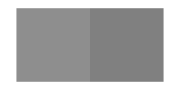

```mathematica
Graphics[{Lighter@Darker@Gray,Rectangle[{0,0},{1,1}],Gray,Rectangle[{1,0},{2,1}]},ImageSize-> Small]
```

### Place Pieces AI

```mathematica
makeAIMove[{},{1,2,3}]
```

{{{1,2,3}},{}}

```mathematica
makeAIMove[{},{1,2}]
```

{{},{1,2}}

```mathematica
makeAIMove[{{1,14,27}},{53,2,3,4}]
```

{{{1,14,27},{2,3,4}},{53}}

### Tile colors

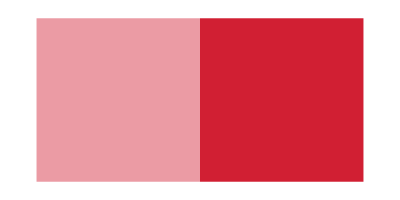

```mathematica
rer=RGBColor[209/255,31/255,51/255];
Graphics[{Lighter@Lighter@rer,Rectangle[{0,0},{1,1}],rer,Rectangle[{1,0},{2,1}]}]
Clear[rer];
```

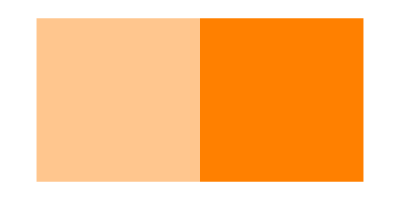

```mathematica
Graphics[{Lighter@Lighter@Orange,Rectangle[{0,0},{1,1}],Orange,Rectangle[{1,0},{2,1}]}]
```

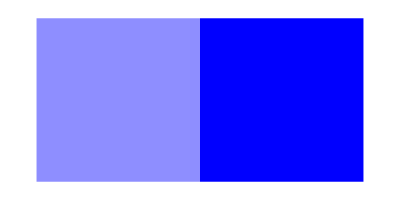

```mathematica
Graphics[{Lighter@Lighter@Blue,Rectangle[{0,0},{1,1}],Blue,Rectangle[{1,0},{2,1}]}]
```

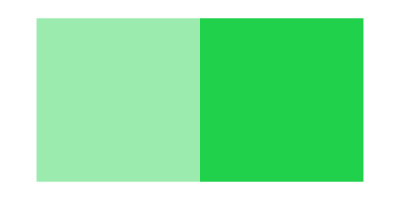

```mathematica
gren=RGBColor[31/255,209/255,75/255];
Graphics[{Lighter@Lighter@gren,Rectangle[{0,0},{1,1}],gren,Rectangle[{1,0},{2,1}]}]
Clear[gren];
```

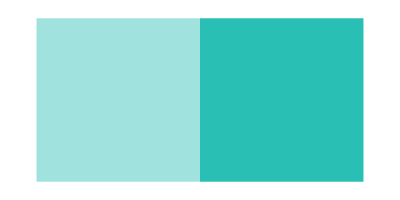

```mathematica
tel=RGBColor[42/255,191/255,181/255];
Graphics[{Lighter@Lighter@tel,Rectangle[{0,0},{1,1}],tel,Rectangle[{1,0},{2,1}]}]
Clear@tel;
```

### drawTile

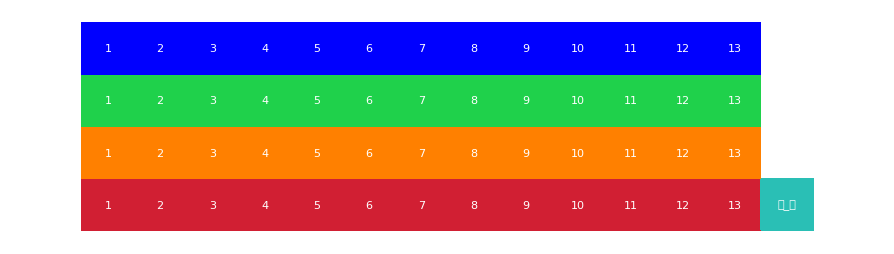

```mathematica
t=Flatten@Table[makeTile[{i-1,j-1},{i,j},i-13+13j,32,"AIGDT"],{i,1,13},{j,1,4}];
AppendTo[t,makeTile[{13,0},{14,1},53,32,"AIDGT"]];
Graphics[{drawTile/@t},PlotRange-> {{0,14},{0,4}}]
Clear[t]
```

### moveTile

```mathematica
b=makeTile[{1,1},{2,2},1,20,"Arial"];
Print@b;
b=moveTile[b,{3,4},{4,3}];
Print@b;
Clear@b;
```

<|x1→1,x2→2,y1→1,y2→2,color→RGBColor[Rational[209, 255], Rational[31, 255], Rational[1, 5]],value→1,fontsize→20,font→Arial|>

<|x1→3,x2→4,y1→3,y2→4,color→RGBColor[Rational[209, 255], Rational[31, 255], Rational[1, 5]],value→1,fontsize→20,font→Arial|>

### Board View Translation

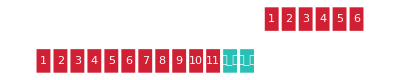

{{1,2,3,4,5,6},{1,2,3,4,5,6,7,8,9,10,11,53,53}}

True

```mathematica
Module[
{board={{1,2,3,4,5,6,7,8,9,10,11,53,53},{4,5,6},{1,2,3}},boardTiles,newboard}
,
boardTiles=convertBoardToView@board;
Print@Graphics[drawTile/@(boardTiles),ImageSize-> 400];
newboard=boardViewToBoard[boardTiles];
Print@newboard;
Print@isLegalBoard@newboard;
]
```

### enoughPoints

```mathematica
(*Place 3 tens and a 1 - 31 pts*)
atLeast30Points[{},convertRackToView[{10,23,36,1}]]
```

True

```mathematica
(*Place 3 tens but keep the 1 - 30 pts*)
atLeast30Points[{1},convertRackToView[{10,23,36,1}]]
```

True

```mathematica
(*Place 3 eights - 24 pts*)
atLeast30Points[{},convertRackToView[{8,21,34}]]
```

False

### input Fields

Two completely separate graphics on top of each other with an input field. Useful for if we want to add names to the people in the game.

```mathematica
CreateWindow@CreateDialog@DynamicModule[
{name="Playa 1"},
Dynamic@Show[{Graphics[{Blue,Rectangle[{-10,-10},{100,100}],White,Text[name,{5,8}]},PlotRange-> {{0,10},{0,10}}],Graphics[Inset[InputField[Dynamic@name,String],{5,5}]]}]
]
```

CreateWindow[qx6eg_shm66FrontEndObject[LinkObject["qx6eg_shm", 3, 1]]6666]